```mathematica
ClearAll["Global`*"];
```

```mathematica
nm=10^-9;
μm=10^-6;
mm=10^-3;
cm=10^-2;
```

```mathematica
n=1;
λ=946nm;
```

```mathematica
Prop[d_]:=({{1, d}, {0, 1}});
Lens[f_]:=({{1, 0}, {-1/f, 1}});
```

```mathematica
(*parameter to q*)
```

```mathematica
q[R_,ω0_]:=1/R-(ⅈ λ)/(n π ω0^2);
ω[z_,ω0_]:=ω0 √(1+((z λ)/(n π ω0^2))^2);
qb[qa_,trans_]:=((trans[[1,1]] qa^-1+trans[[1,2]])/(trans[[2,1]] qa^-1+trans[[2,2]]))^-1;
```

```mathematica
(*q to parameter*)
```

```mathematica
z[q_]:=-Re[q]/Abs[q]^2;
zR[q_]:=-Im[q]/Abs[q]^2;
ω0[q_]:=√((λ zR[q])/(n π));
ωspot[q_]:=√(-λ/(n π Im[q]));
Curve[qa_,z0_,zcur_]:=ω0[qa] √(1+((zcur-z[qa]-z0)/zR[qa])^2);
```

```mathematica
(*calculation*)
```

```mathematica
{{Manipulator[Dynamic[di]],Dynamic[di]},
{Manipulator[Dynamic[d1]],Dynamic[d1]},
{Manipulator[Dynamic[d2]],Dynamic[d2]},
{Manipulator[Dynamic[d3]],Dynamic[d3]},
{Manipulator[Dynamic[d4]],Dynamic[d4]}}//MatrixForm
```

( | 
 | 
 | 
 | 
 | )

```mathematica
Dynamic[
f1=50mm;
f2=500mm;
f3=100mm;
f4=100mm;
qia=q[Infinity,3.082μm];
graphi=Plot[Curve[qia,0,zcur],{zcur,0,di},PlotRange->All];
qib=qb[qia,Prop[di]];
q1a=qb[qib,Lens[f1]];
graph1=Plot[Curve[q1a,di,zcur],{zcur,di,di+d1},PlotRange->All];
q1b=qb[q1a,Prop[d1]];
q2a=qb[q1b,Lens[f2]];
graph2=Plot[Curve[q2a,(di+d1),zcur],{zcur,(di+d1),(di+d1+d2)},PlotRange->All];
q2b=qb[q2a,Prop[d2]];
q3a=qb[q2b,Lens[f3]];
graph3=Plot[Curve[q3a,(di+d1+d2),zcur],{zcur,(di+d1+d2),(di+d1+d2+d3)},PlotRange->All];
q3b=qb[q3a,Prop[d3]];
q4a=qb[q3b,Lens[f4]];
graph4=Plot[Curve[q4a,(di+d1+d2+d3),zcur],{zcur,(di+d1+d2+d3),(di+d1+d2+d3+d4)},PlotRange->All];
q4b=qb[q4a,Prop[d4]];
Show[{graphi,graph1,graph2(*,graph3,graph4*)}]]
```

```mathematica
Dynamic[1000000*ω0[q1b]]
Dynamic[1000000*ω0[q2b]]
```

```mathematica
Dynamic@ωspot@qib
```

```mathematica
12.7/1.414
```

8.98161

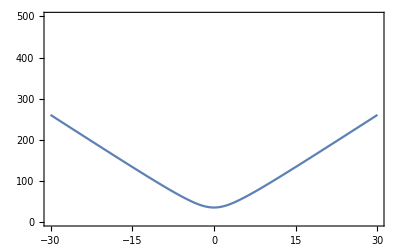

```mathematica
Plot[N[35μm √(1+((zz mm λ)/(n π (35μm)^2))^2)]/μm,{zz,-30,30},PlotRange->{0,500},Frame->True]
```

```mathematica
38/4.51*8
```

67.4058